```mathematica
Quit[]
```

```mathematica
SetDirectory["~/Documents/Univ/hybrid_metric-Palatini/math"];
```

```mathematica
$Assumptions={Mp>0,δ>0,ξg>0,ξΓ>0,ρJ>0,ρ2>0,Mp^2 δ-(ξg+ξΓ)ρ2>0};
```

```mathematica
coord={h1,h2,h3,h4};
n=Length[coord];
(*4 d.o.f.*)
```

```mathematica
metric=IdentityMatrix[n]/(1+(ξg/δ+ξΓ/δ)(coord.coord)/Mp^2)+(6 ξg/δ(2 ξΓ/δ+ξg/δ+ξΓ/δ(ξΓ/δ+ξg/δ)(coord.coord)/Mp^2))/((1+ξΓ/δ (coord.coord)/Mp^2)(1+(ξg/δ+ξΓ/δ)(coord.coord)/Mp^2)^2)Table[(coord[[i]]coord[[j]])/Mp^2,{i,n},{j,n}]//Simplify;
(*δ -> 0 corresponds to ξ -> ∞*)
```

```mathematica
inversemetric=Simplify[Inverse[metric]];
affine:=affine=Table[(1/2)*Sum[(inversemetric[[i,s]])*(D[metric[[s,j]],coord[[k]]]+D[metric[[s,k]],coord[[j]]]-D[metric[[j,k]],coord[[s]]]),{s,1,n}],{i,1,n},{j,1,n},{k,1,n}]
listaffine:=Table[If[UnsameQ[affine[[i,j,k]],0],{ToString[Γ[i,j,k]],affine[[i,j,k]]}],{i,1,n},{j,1,n},{k,1,j}]
TableForm[Partition[DeleteCases[Flatten[listaffine],Null],2],TableSpacing->{2,2}]
riemann:=riemann=Table[D[affine[[i,j,l]],coord[[k]]]-D[affine[[i,j,k]],coord[[l]]]+Sum[affine[[s,j,l]]affine[[i,k,s]]-affine[[s,j,k]]affine[[i,l,s]],{s,1,n}],{i,1,n},{j,1,n},{k,1,n},{l,1,n}]
listriemann:=Table[If[UnsameQ[riemann[[i,j,k,l]],0],{ToString[R[i,j,k,l]],riemann[[i,j,k,l]]}],{i,1,n},{j,1,n},{k,1,n},{l,1,k-1}]
TableForm[Partition[DeleteCases[Flatten[listriemann],Null],2],TableSpacing->{2,2}]
ricci:=ricci=Table[Sum[riemann[[i,j,i,l]],{i,1,n}],{j,1,n},{l,1,n}]
listricci:=Table[If[UnsameQ[ricci[[j,l]],0],{ToString[R[j,l]],ricci[[j,l]]}],{j,1,n},{l,1,j}]
TableForm[Partition[DeleteCases[Flatten[listricci],Null],2],TableSpacing->{2,2}]
scalar=Sum[inversemetric[[i,j]]ricci[[i,j]],{i,1,n},{j,1,n}]/.{h2->0,h3->0,h4->0,h1->h}//Simplify
(*follow Hartle's book*)
```

(6 (h^8 (δ+6 ξg)^2 ξΓ^2 (ξg+ξΓ)^3+4 Mp^8 δ^5 (δ (ξg+ξΓ)+3 ξg (ξg+2 ξΓ))+h^6 Mp^2 δ (δ+6 ξg) ξΓ (ξg+ξΓ)^2 (6 ξg (2 ξg+5 ξΓ)+δ (2 ξg+7 ξΓ))+h^2 Mp^6 δ^3 (δ+6 ξg) (6 ξg (ξg+2 ξΓ)^2+δ (5 ξg^2+18 ξg ξΓ+13 ξΓ^2))+h^4 Mp^4 δ^2 (δ+6 ξg) (ξg+ξΓ) (6 ξg (ξg^2+6 ξg ξΓ+8 ξΓ^2)+δ (ξg^2+12 ξg ξΓ+15 ξΓ^2))))/(δ (Mp^5 δ^3+h^4 Mp (δ+6 ξg) ξΓ (ξg+ξΓ)+h^2 Mp^3 δ (δ+6 ξg) (ξg+2 ξΓ))^2)

```mathematica
Λorigin[ξg_,ξΓ_]=(Mp^2 scalar/.{h->0,δ->1})^(-1/2)
(*cutoff from Ricci scalar at origin*)
```

1/(2 √6 √(ξg+ξΓ+3 ξg (ξg+2 ξΓ)))

```mathematica
Eigenvalues[metric]//Simplify
(*check 1 radial eigenvalue and 3 angular eigenvalues*)
```

{(Mp^2 δ)/(Mp^2 δ+(h1^2+h2^2+h3^2+h4^2) (ξg+ξΓ)),(Mp^2 δ)/(Mp^2 δ+(h1^2+h2^2+h3^2+h4^2) (ξg+ξΓ)),(Mp^2 δ)/(Mp^2 δ+(h1^2+h2^2+h3^2+h4^2) (ξg+ξΓ)),(Mp^6 δ^3+(h1^2+h2^2+h3^2+h4^2)^2 Mp^2 (δ+6 ξg) ξΓ (ξg+ξΓ)+(h1^2+h2^2+h3^2+h4^2) Mp^4 δ (δ+6 ξg) (ξg+2 ξΓ))/((Mp^2 δ+(h1^2+h2^2+h3^2+h4^2) ξΓ) (Mp^2 δ+(h1^2+h2^2+h3^2+h4^2) (ξg+ξΓ))^2)}

```mathematica
F2[ρJ_]=Eigenvalues[metric][[4]]/.{h2->0,h3->0,h4->0,h1->ρJ}//Simplify
ρinρJ[ρJ_]=Sqrt[ρJ^2 Eigenvalues[metric][[1]]/.{h2->0,h3->0,h4->0,h1->ρJ}]//Simplify
```

(Mp^6 δ^3+Mp^4 δ (δ+6 ξg) (ξg+2 ξΓ) ρJ^2+Mp^2 (δ+6 ξg) ξΓ (ξg+ξΓ) ρJ^4)/((Mp^2 δ+ξΓ ρJ^2) (Mp^2 δ+(ξg+ξΓ) ρJ^2)^2)

Mp ρJ √(δ/(Mp^2 δ+(ξg+ξΓ) ρJ^2))

```mathematica
dzdρJ[ρJ_]=Sqrt[F2[ρJ]-ρinρJ'[ρJ]^2]//Simplify
```

√((2 Mp^6 δ^2 (δ (ξg+ξΓ)+3 ξg (ξg+2 ξΓ)) ρJ^2+Mp^4 δ (δ+6 ξg) (ξg^2+4 ξg ξΓ+3 ξΓ^2) ρJ^4+Mp^2 (δ+6 ξg) ξΓ (ξg+ξΓ)^2 ρJ^6)/((Mp^2 δ+ξΓ ρJ^2) (Mp^2 δ+(ξg+ξΓ) ρJ^2)^3))

```mathematica
ρJinρ2[ρ2_]=Sqrt[ρ2/(1-(ξg/δ+ξΓ/δ)ρ2/Mp^2)];
```

```mathematica
ρinρJ[ρJinρ2[ρ2]]^2//Simplify
(*check the inverse function*)
```

ρ2

```mathematica
dzdρ2[ρ2_]=dzdρJ[ρJinρ2[ρ2]]ρJinρ2'[ρ2]//Simplify
```

1/2 (1/(Mp^2 δ-(ξg+ξΓ) ρ2))^(3/2) √(((Mp^2 δ-(ξg+ξΓ) ρ2) (2 Mp^4 δ (δ (ξg+ξΓ)+3 ξg (ξg+2 ξΓ))-Mp^2 (ξg+ξΓ) (6 ξg (ξg+ξΓ)+δ (3 ξg+ξΓ)) ρ2+ξg (ξg+ξΓ)^2 ρ2^2))/(Mp^2 δ-ξg ρ2))

```mathematica
AbsoluteTiming[dρ2dz[ρ2_]=(dzdρ2[ρ2])^-1;
d2ρ2dz2[ρ2_]=(dzdρ2[ρ2])^-1 dρ2dz'[ρ2];
d3ρ2dz3[ρ2_]=(dzdρ2[ρ2])^-1 d2ρ2dz2'[ρ2];
d4ρ2dz4[ρ2_]=(dzdρ2[ρ2])^-1 d3ρ2dz3'[ρ2];
d5ρ2dz5[ρ2_]=(dzdρ2[ρ2])^-1 d4ρ2dz4'[ρ2];
d6ρ2dz6[ρ2_]=(dzdρ2[ρ2])^-1 d5ρ2dz5'[ρ2];
d7ρ2dz7[ρ2_]=(dzdρ2[ρ2])^-1 d6ρ2dz6'[ρ2];
d8ρ2dz8[ρ2_]=(dzdρ2[ρ2])^-1 d7ρ2dz7'[ρ2];
d9ρ2dz9[ρ2_]=(dzdρ2[ρ2])^-1 d8ρ2dz8'[ρ2];
d10ρ2dz10[ρ2_]=(dzdρ2[ρ2])^-1 d9ρ2dz9'[ρ2];]
```

{391.239,Null}

```mathematica
ρ2inz[z_]=dρ2dz[0]z+1/(2!)d2ρ2dz2[0] z^2+1/(3!)d3ρ2dz3[0] z^3+1/(4!)d4ρ2dz4[0] z^4+1/(5!)d5ρ2dz5[0] z^5+1/(6!)d6ρ2dz6[0] z^6+1/(7!)d7ρ2dz7[0] z^7+1/(8!)d8ρ2dz8[0] z^8+1/(9!)d9ρ2dz9[0] z^9+1/(10!)z^10 d10ρ2dz10[0]//Simplify;//AbsoluteTiming
```

{2956.22,Null}

```mathematica
Export["rho2inz.wdx",ρ2inz[z]];
```

```mathematica
ρ2inz[z_]=Import["rho2inz.wdx"];
```

```mathematica
Usur[ρ_,z_]=λt/4(ρ^2-ρ2inz[z])^2;
```

```mathematica
Λ23=(D[Usur[ρ,z],{ρ,2},{z,3}]/.{ρ->0,z->0})^-1;
Λ05=(D[Usur[ρ,z],{ρ,0},{z,5}]/.{ρ->0,z->0})^-1;
Λ242=(D[Usur[ρ,z],{ρ,2},{z,4}]/.{ρ->0,z->0})^-1;
Λ062=(D[Usur[ρ,z],{ρ,0},{z,6}]/.{ρ->0,z->0})^-1;
Λ253=(D[Usur[ρ,z],{ρ,2},{z,5}]/.{ρ->0,z->0})^-1;
Λ073=(D[Usur[ρ,z],{ρ,0},{z,7}]/.{ρ->0,z->0})^-1;
Λ264=(D[Usur[ρ,z],{ρ,2},{z,6}]/.{ρ->0,z->0})^-1;
Λ084=(D[Usur[ρ,z],{ρ,0},{z,8}]/.{ρ->0,z->0})^-1;
Λ275=(D[Usur[ρ,z],{ρ,2},{z,7}]/.{ρ->0,z->0})^-1;
Λ095=(D[Usur[ρ,z],{ρ,0},{z,9}]/.{ρ->0,z->0})^-1;
Λ286=(D[Usur[ρ,z],{ρ,2},{z,8}]/.{ρ->0,z->0})^-1;
Λ0t6=(D[Usur[ρ,z],{ρ,0},{z,10}]/.{ρ->0,z->0})^-1;
(*calculate Λnmp = Subscript[Λ, ρ^n z^m]^p. t = 10*)
```

```mathematica
Simplify[Normal[Series[Λ23,{δ,0,-1}]],{δ>0,ξg>0,ξΓ>0}]
Simplify[Normal[Series[Λ05,{δ,0,-2}]],{δ>0,ξg>0,ξΓ>0}]
Simplify[Normal[Series[Λ242,{δ,0,-1}]],{δ>0,ξg>0,ξΓ>0}]
Simplify[Normal[Series[Λ062,{δ,0,-2}]],{δ>0,ξg>0,ξΓ>0}]
Simplify[Normal[Series[Λ253,{δ,0,-1}]],{δ>0,ξg>0,ξΓ>0}]
Simplify[Normal[Series[Λ073,{δ,0,-2}]],{δ>0,ξg>0,ξΓ>0}]
Simplify[Normal[Series[Λ264,{δ,0,-1}]],{δ>0,ξg>0,ξΓ>0}]
Simplify[Normal[Series[Λ084,{δ,0,-2}]],{δ>0,ξg>0,ξΓ>0}]
Simplify[Normal[Series[Λ275,{δ,0,-1}]],{δ>0,ξg>0,ξΓ>0}]
Simplify[Normal[Series[Λ095,{δ,0,-2}]],{δ>0,ξg>0,ξΓ>0}]
Simplify[Normal[Series[Λ286,{δ,0,-1}]],{δ>0,ξg>0,ξΓ>0}]
Simplify[Normal[Series[Λ0t6,{δ,0,-2}]],{δ>0,ξg>0,ξΓ>0}]
(*check their ξ -> ∞ or δ -> 0 behaviors*)
```

-(3 √(3/2) Mp ξg^(3/2) (ξg+2 ξΓ)^(7/2))/(2 δ λt (ξg+ξΓ) (ξg^3+5 ξg^2 ξΓ+7 ξg ξΓ^2+ξΓ^3))

-(3 √(3/2) Mp ξg^(5/2) (ξg+2 ξΓ)^(11/2))/(5 δ^2 λt (ξg+ξΓ) (2 ξg^5+16 ξg^4 ξΓ+47 ξg^3 ξΓ^2+59 ξg^2 ξΓ^3+25 ξg ξΓ^4+ξΓ^5))

(9 Mp^2 ξg^2 (ξg+2 ξΓ)^5)/(2 δ λt (ξg+ξΓ) (2 ξg^5+16 ξg^4 ξΓ+47 ξg^3 ξΓ^2+59 ξg^2 ξΓ^3+21 ξg ξΓ^4-3 ξΓ^5))

(27 Mp^2 ξg^3 (ξg+2 ξΓ)^7)/(δ^2 λt (124 ξg^8+1488 ξg^7 ξΓ+7440 ξg^6 ξΓ^2+19900 ξg^5 ξΓ^3+30335 ξg^4 ξΓ^4+25638 ξg^3 ξΓ^5+10654 ξg^2 ξΓ^6+1420 ξg ξΓ^7-107 ξΓ^8))

-(9 √(3/2) Mp^3 ξg^(5/2) (ξg+2 ξΓ)^(13/2))/(2 δ λt (ξg+ξΓ)^2 (2 ξg^6+20 ξg^5 ξΓ+78 ξg^4 ξΓ^2+144 ξg^3 ξΓ^3+124 ξg^2 ξΓ^4+22 ξg ξΓ^5-ξΓ^6))

-(9 √(3/2) Mp^3 ξg^(7/2) (ξg+2 ξΓ)^(17/2))/(14 δ^2 λt (ξg+ξΓ)^2 (6 ξg^8+78 ξg^7 ξΓ+423 ξg^6 ξΓ^2+1224 ξg^5 ξΓ^3+1989 ξg^4 ξΓ^4+1730 ξg^3 ξΓ^5+633 ξg^2 ξΓ^6+40 ξg ξΓ^7+3 ξΓ^8))

(27 Mp^4 ξg^3 (ξg+2 ξΓ)^8)/(2 δ λt (ξg+ξΓ)^2 (4 ξg^8+52 ξg^7 ξΓ+282 ξg^6 ξΓ^2+816 ξg^5 ξΓ^3+1286 ξg^4 ξΓ^4+1100 ξg^3 ξΓ^5+382 ξg^2 ξΓ^6+60 ξg ξΓ^7+57 ξΓ^8))

(81 Mp^4 ξg^4 (ξg+2 ξΓ)^10)/(2 δ^2 λt (ξg+ξΓ)^2 (508 ξg^10+8128 ξg^9 ξΓ+56388 ξg^8 ξΓ^2+220724 ξg^7 ξΓ^3+530219 ξg^6 ξΓ^4+790530 ξg^5 ξΓ^5+702385 ξg^4 ξΓ^6+322300 ξg^3 ξΓ^7+49629 ξg^2 ξΓ^8-1550 ξg ξΓ^9+1381 ξΓ^10))

-(27 √(3/2) Mp^5 ξg^(7/2) (ξg+2 ξΓ)^(19/2))/(8 δ λt (ξg+ξΓ)^3 (ξg^9+15 ξg^8 ξΓ+96 ξg^7 ξΓ^2+338 ξg^6 ξΓ^3+720 ξg^5 ξΓ^4+804 ξg^4 ξΓ^5+403 ξg^3 ξΓ^6-111 ξg^2 ξΓ^7-150 ξg ξΓ^8-38 ξΓ^9))

-((27 √(3/2) Mp^5 ξg^(9/2) (ξg+2 ξΓ)^(23/2))/(20 δ^2 λt (ξg+ξΓ)^3 (34 ξg^11+612 ξg^10 ξΓ+4845 ξg^9 ξΓ^2+22049 ξg^8 ξΓ^3+63138 ξg^7 ξΓ^4+116880 ξg^6 ξΓ^5+136420 ξg^5 ξΓ^6+92910 ξg^4 ξΓ^7+28638 ξg^3 ξΓ^8+406 ξg^2 ξΓ^9-963 ξg ξΓ^10-321 ξΓ^11)))

(81 Mp^6 ξg^4 (ξg+2 ξΓ)^11)/(8 δ λt (ξg+ξΓ)^3 (2 ξg^11+36 ξg^10 ξΓ+285 ξg^9 ξΓ^2+1297 ξg^8 ξΓ^3+3630 ξg^7 ξΓ^4+7236 ξg^6 ξΓ^5+9176 ξg^5 ξΓ^6+7422 ξg^4 ξΓ^7+3519 ξg^3 ξΓ^8+623 ξg^2 ξΓ^9-426 ξg ξΓ^10-366 ξΓ^11))

(243 Mp^6 ξg^5 (ξg+2 ξΓ)^13)/(4 δ^2 λt (ξg+ξΓ)^3 (2044 ξg^13+42924 ξg^12 ξΓ+404712 ξg^11 ξΓ^2+2253508 ξg^10 ξΓ^3+8192911 ξg^9 ξΓ^4+20245377 ξg^8 ξΓ^5+34391498 ξg^7 ξΓ^6+39281540 ξg^6 ξΓ^7+28592460 ξg^5 ξΓ^8+11761734 ξg^4 ξΓ^9+2185444 ξg^3 ξΓ^10+309582 ξg^2 ξΓ^11+126437 ξg ξΓ^12-5519 ξΓ^13))

```mathematica
Simplify[Normal[Series[Λ23/.{ξΓ->0},{δ,0,-1}]],{ξg>0,δ>0}]
Simplify[Normal[Series[Λ05/.{ξΓ->0},{δ,0,-2}]],{ξg>0,δ>0}]
Simplify[Normal[Series[Λ242/.{ξΓ->0},{δ,0,-1}]],{ξg>0,δ>0}]
Simplify[Normal[Series[Λ062/.{ξΓ->0},{δ,0,-2}]],{ξg>0,δ>0}]
Simplify[Normal[Series[Λ253/.{ξΓ->0},{δ,0,-1}]],{ξg>0,δ>0}]
Simplify[Normal[Series[Λ073/.{ξΓ->0},{δ,0,-2}]],{ξg>0,δ>0}]
Simplify[Normal[Series[Λ264/.{ξΓ->0},{δ,0,-1}]],{ξg>0,δ>0}]
Simplify[Normal[Series[Λ084/.{ξΓ->0},{δ,0,-2}]],{ξg>0,δ>0}]
Simplify[Normal[Series[Λ275/.{ξΓ->0},{δ,0,-1}]],{ξg>0,δ>0}]
Simplify[Normal[Series[Λ095/.{ξΓ->0},{δ,0,-2}]],{ξg>0,δ>0}]
Simplify[Normal[Series[Λ286/.{ξΓ->0},{δ,0,-1}]],{ξg>0,δ>0}]
Simplify[Normal[Series[Λ0t6/.{ξΓ->0},{δ,0,-2}]],{ξg>0,δ>0}]
(*check their metric-limit*)
```

-(3 √(3/2) Mp ξg)/(2 δ λt)

-(3 √(3/2) Mp ξg^2)/(10 δ^2 λt)

(9 Mp^2 ξg)/(4 δ λt)

(27 Mp^2 ξg^2)/(124 δ^2 λt)

-(9 √(3/2) Mp^3 ξg)/(4 δ λt)

-(3 √(3/2) Mp^3 ξg^2)/(28 δ^2 λt)

(27 Mp^4 ξg)/(8 δ λt)

(81 Mp^4 ξg^2)/(1016 δ^2 λt)

-(27 √(3/2) Mp^5 ξg)/(8 δ λt)

-(27 √(3/2) Mp^5 ξg^2)/(680 δ^2 λt)

(81 Mp^6 ξg)/(16 δ λt)

(243 Mp^6 ξg^2)/(8176 δ^2 λt)

```mathematica
Simplify[Normal[Series[Λ23/.{ξg->0},{δ,0,5}]],{δ>0,ξΓ>0}]
Simplify[Normal[Series[Λ05/.{ξg->0},{δ,0,5}]],{δ>0,ξΓ>0}]
Simplify[Normal[Series[Λ242/.{ξg->0},{δ,0,5}]],{δ>0,ξΓ>0}]
Simplify[Normal[Series[Λ062/.{ξg->0},{δ,0,5}]],{δ>0,ξΓ>0}]
Simplify[Normal[Series[Λ253/.{ξg->0},{δ,0,5}]],{δ>0,ξΓ>0}]
Simplify[Normal[Series[Λ073/.{ξg->0},{δ,0,5}]],{δ>0,ξΓ>0}]
Simplify[Normal[Series[Λ264/.{ξg->0},{δ,0,5}]],{δ>0,ξΓ>0}]
Simplify[Normal[Series[Λ084/.{ξg->0},{δ,0,5}]],{δ>0,ξΓ>0}]
Simplify[Normal[Series[Λ275/.{ξg->0},{δ,0,5}]],{δ>0,ξΓ>0}]
Simplify[Normal[Series[Λ095/.{ξg->0},{δ,0,5}]],{δ>0,ξΓ>0}]
Simplify[Normal[Series[Λ286/.{ξg->0},{δ,0,5}]],{δ>0,ξΓ>0}]
Simplify[Normal[Series[Λ0t6/.{ξg->0},{δ,0,5}]],{δ>0,ξΓ>0}]
(*check their Palatini-limit*)
```

-(√2 Mp √(δ/ξΓ))/λt

-(4 √2 Mp √(δ/ξΓ))/(15 λt)

-(4 Mp^2 δ)/(3 λt ξΓ)

-(16 Mp^2 δ)/(107 λt ξΓ)

(4 √2 Mp^3 (δ/ξΓ)^(3/2))/λt

-(8 √2 Mp^3 (δ/ξΓ)^(3/2))/(63 λt)

(16 Mp^4 δ^2)/(57 λt ξΓ^2)

(32 Mp^4 δ^2)/(1381 λt ξΓ^2)

(2 √2 Mp^5 (δ/ξΓ)^(5/2))/(19 λt)

(16 √2 Mp^5 (δ/ξΓ)^(5/2))/(4815 λt)

-(8 Mp^6 δ^3)/(183 λt ξΓ^3)

-(64 Mp^6 δ^3)/(5519 λt ξΓ^3)

```mathematica
ξΓCOBE[ξg_]=ξΓ/.Solve[calPz==1/((1+6ξg)(ξg+ξΓ))λ NN^2/(12 π^2),ξΓ,Assumptions->{}][[1]]/.{λ->1/100,NN->55,calPz->21 10^-10};
(*COBE normalization*)
```

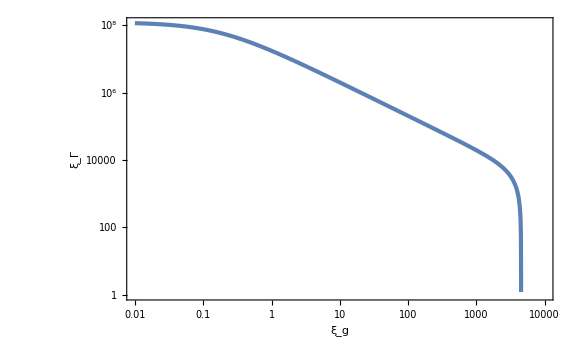

```mathematica
LogLogPlot[ξΓCOBE[ξg],{ξg,10^-2,10^4},FrameLabel->{Subscript[ξ, g],Subscript[ξ, Γ]}]
```

```mathematica
zinρ2[ρ2_]:=NIntegrate[dzdρ2[ρ2p]/.{δ->1,Mp->1,ξΓ->ξΓCOBE[100],ξg->100}//Simplify,{ρ2p,0,ρ2}]
```

```mathematica
zinρ2[4 10^-6]
```

0.0549535

```mathematica
zinρ2List=ParallelTable[{ρ2,zinρ2[ρ2]},{ρ2,0,4 10^-6,10^-8}];
```

```mathematica
zinρ2int[ρ2_]=Interpolation[zinρ2List][ρ2];
```

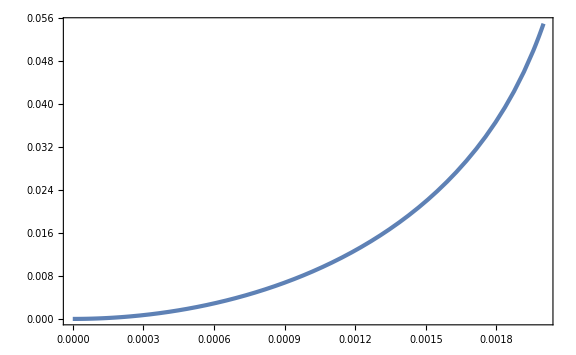

```mathematica
Plot[zinρ2int[ρ^2],{ρ,0,2 10^-3}]
```

```mathematica
ParametricPlot3D[{r Cos[θ],r Sin[θ],zinρ2int[r^2/100]},{r,0,2 10^-2},{θ,0,2π},Boxed->False,Axes->False,PlotStyle->None]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{r Cos[θ],r Sin[θ],zinρ2int[r^2/100]},{r,0,2 10^-2},{θ,0,2π},Boxed->False,Ticks->None,AxesStyle->Directive[Black,Thick],AxesLabel->{Subscript[OverTilde[ϕ], 1],Subscript[OverTilde[ϕ], 2],σ}]
```

-Graphics3D-

```mathematica
ξgc=ξg/.Solve[ξΓCOBE[ξg]==0,ξg,Assumptions->{}][[2]];ξgc//N
(*ξg in the metric limit*)
```

4502.24

```mathematica
Λ23COBE[ξg_]=Abs[Λ23/Mp]/.{λt->1/100,ξΓ->ξΓCOBE[ξg],δ->1,Mp->1};
Λ05COBE[ξg_]=Abs[Λ05/Mp]/.{λt->1/100,ξΓ->ξΓCOBE[ξg],δ->1,Mp->1};
Λ24COBE[ξg_]=Sqrt[Abs[Λ242/Mp^2]]/.{λt->1/100,ξΓ->ξΓCOBE[ξg],δ->1,Mp->1};
Λ06COBE[ξg_]=Sqrt[Abs[Λ062/Mp^2]]/.{λt->1/100,ξΓ->ξΓCOBE[ξg],δ->1,Mp->1};
Λ25COBE[ξg_]=Abs[Λ253/Mp^3]^(1/3)/.{λt->1/100,ξΓ->ξΓCOBE[ξg],δ->1,Mp->1};
Λ07COBE[ξg_]=Abs[Λ073/Mp^3]^(1/3)/.{λt->1/100,ξΓ->ξΓCOBE[ξg],δ->1,Mp->1};
Λ26COBE[ξg_]=Abs[Λ264/Mp^4]^(1/4)/.{λt->1/100,ξΓ->ξΓCOBE[ξg],δ->1,Mp->1};
Λ08COBE[ξg_]=Abs[Λ084/Mp^4]^(1/4)/.{λt->1/100,ξΓ->ξΓCOBE[ξg],δ->1,Mp->1};
Λ27COBE[ξg_]=Abs[Λ275/Mp^5]^(1/5)/.{λt->1/100,ξΓ->ξΓCOBE[ξg],δ->1,Mp->1};
Λ09COBE[ξg_]=Abs[Λ095/Mp^5]^(1/5)/.{λt->1/100,ξΓ->ξΓCOBE[ξg],δ->1,Mp->1};
Λ28COBE[ξg_]=Abs[Λ286/Mp^6]^(1/6)/.{λt->1/100,ξΓ->ξΓCOBE[ξg],δ->1,Mp->1};
Λ0tCOBE[ξg_]=Abs[Λ0t6/Mp^6]^(1/6)/.{λt->1/100,ξΓ->ξΓCOBE[ξg],δ->1,Mp->1};
(*cutoff w/ COBE normalization*)
```

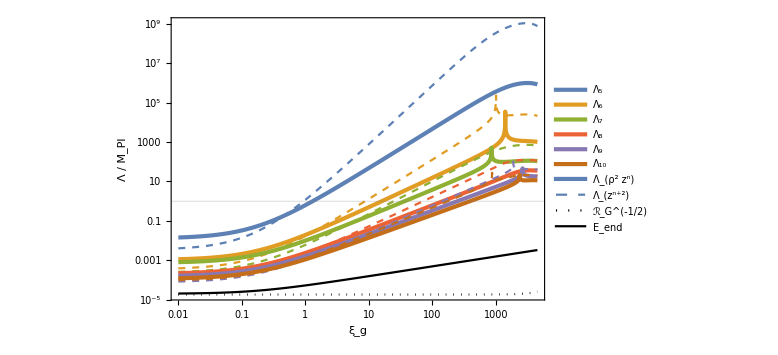

```mathematica
LogLogPlot[{Λ23COBE[ξg],Λ05COBE[ξg],Λ24COBE[ξg],Λ06COBE[ξg],Λ25COBE[ξg],Λ07COBE[ξg],Λ26COBE[ξg],Λ08COBE[ξg],Λ27COBE[ξg],Λ09COBE[ξg],Λ28COBE[ξg],Λ0tCOBE[ξg],0,0,Λorigin[ξg,ξΓCOBE[ξg]],(λ/4)^(1/4)1/Sqrt[ξg+ξΓCOBE[ξg]]/.{λ->1/100}},{ξg,10^-2,ξgc},GridLines->{None,{1}},PlotStyle->{{Color[1],AbsoluteThickness[3]},{Color[1],Dashed},
{Color[2],AbsoluteThickness[3]},{Color[2],Dashed},
{Color[3],AbsoluteThickness[3]},{Color[3],Dashed},
{Color[4],AbsoluteThickness[3]},{Color[4],Dashed},
{Color[5],AbsoluteThickness[3]},{Color[5],Dashed},
{Color[6],AbsoluteThickness[3]},{Color[6],Dashed},
{Color[1],AbsoluteThickness[3]},{Color[1],Dashed},
{Black,Dotted},{Black}},FrameLabel->{Subscript[ξ, g],"Λ / M_Pl"},PlotLegends->Placed[LineLegend[{Subscript[Λ, 5],None,Subscript[Λ, 6],None,Subscript[Λ, 7],None,Subscript[Λ, 8],None,Subscript[Λ, 9],None,Subscript[Λ, 10],None,Subscript[Λ, ρ^2 z^("n")],Subscript[Λ, z^("n"+2)],"ℛ_G^(-1/2)","E_end"},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"],LegendLayout->"Row",LegendMarkerSize->20],{0.37,0.82}],FrameTicks->{{{{10^-5,"",0.005},{10^-4,"",0.005},{10^-3,"10^-3"},{10^-2,"",0.005},{10^-1,"",0.005},{10^0,"1"},{10^1,"",0.005},{10^2,"",0.005},{10^3,"10^3"},{10^4,"",0.005},{10^5,"",0.005},{10^6,"10^6"},{10^7,"",0.005},{10^8,"",0.005},{10^9,"10^9"}},{{10^-5,"",0.005},{10^-4,"",0.005},{10^-3,""},{10^-2,"",0.005},{10^-1,"",0.005},{10^0,""},{10^1,"",0.005},{10^2,"",0.005},{10^3,""},{10^4,"",0.005},{10^5,"",0.005},{10^6,""},{10^7,"",0.005},{10^8,"",0.005},{10^9,""}}},Automatic}]
```

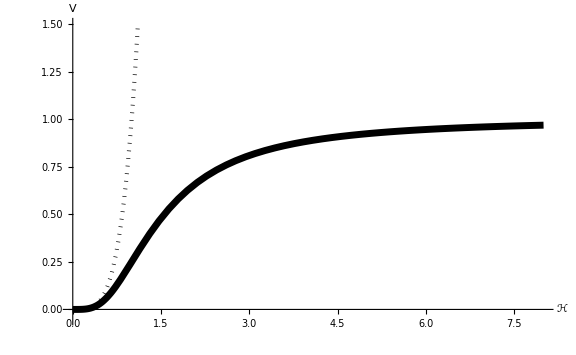

```mathematica
Plot[{x^4,x^4/((1+x^2)^2)},{x,0,8},PlotRange->{-0.05,1.5},Frame->False,Ticks->None,AxesStyle->Directive[Thick,Black],PlotStyle->{{Black,Dotted,AbsoluteThickness[3]},{Black,AbsoluteThickness[5]}},AxesLabel->{ℋ,V}]
```

```mathematica
(6 2)/55^2//N
```

0.00396694